```mathematica
Rx[α_]:=({{1, 0, 0}, {0, Cos[α], Sin[α]}, {0, -Sin[α], Cos[α]}});
Ry[α_]:=({{Cos[α], 0, -Sin[α]}, {0, 1, 0}, {Sin[α], 0, Cos[α]}});
R[t_]:=({{Exp[-t*R2p], 0, 0}, {0, Exp[-t*R1p], 0}, {0, 0, Exp[-t*R2p]}});
R90[β_]:=Rx[β];
R180[β_]:=Ry[2*β];
SL1[t_]:=Rx[-θ].R[t].Ry[ω*t].Rx[θ];
SL2[t_]:=Rx[θ-Pi].R[t].Ry[ω*t].Rx[Pi-θ];
(* SL: standard *)
SSL:=Part[Part[R90[-β].SL1[t].R90[β].({{0}, {0}, {1}}),3],1];
(* SL: rotary-echo *)
RESL:=Part[Part[R90[-β].SL2[t/2].SL1[t/2].R90[β].({{0}, {0}, {1}}),3],1];
(* SL: composite *)
CSL:=Part[Part[R90[β].SL2[t/2].R180[β].SL1[t/2].R90[β].({{0}, {0}, {1}}),3],1];
(* SL: paired-self-compensated *)
PSCSL:=Part[Part[R90[-β].SL2[t/4].SL1[t/4].R180[β].SL2[t/4].SL1[t/4].R90[β].({{0}, {0}, {1}}),3],1];
(* SL: totally-balanced *)
TBSL:=Part[Part[R90[-β].SL1[t/4].R180[-β].SL2[t/2].R180[β].SL1[t/4].R90[β].({{0}, {0}, {1}}),3],1];
(* SL: Triple-refocused *)
TRSL:=Part[Part[R90[β].SL2[t/4].R180[-β].SL1[t/4].R180[β].SL2[t/4].R180[β].SL1[t/4].R90[β].({{0}, {0}, {1}}),3],1];
(* SL: Quqa-refocused *)
QRSL:=Part[Part[R90[-β].SL1[t/8].R180[-β].SL2[t/4].R180[β].SL1[t/4].R180[β].SL2[t/4].R180[-β].SL1[t/8].R90[β].({{0}, {0}, {1}}),3],1];
CSL/.θ->0//FullSimplify
TBSL/.θ->0//FullSimplify
TRSL/.θ->0//FullSimplify
QRSL/.θ->0//FullSimplify
```

ⅇ^(-R2p t) Cos[β]^2 Cos[2 β]-ⅇ^(-R1p t) Sin[β]^2

ⅇ^(-R2p t) Cos[β]^2+ⅇ^(-R1p t) Sin[β]^2

ⅇ^(-R2p t) Cos[β]^2 Cos[2 β]-ⅇ^(-R1p t) Sin[β]^2

ⅇ^(-R2p t) Cos[β]^2+ⅇ^(-R1p t) Sin[β]^2

```mathematica
CSL/.β->Pi/2//FullSimplify
TBSL/.β->Pi/2//FullSimplify
TRSL/.β->Pi/2//FullSimplify
QRSL/.β->Pi/2//FullSimplify
```

-ⅇ^(-R1p t) Cos[θ]^2-ⅇ^(-R2p t) Sin[θ]^2

ⅇ^(-R1p t) Cos[θ]^2+ⅇ^(-R2p t) Sin[θ]^2

-ⅇ^(-R1p t) Cos[θ]^2-ⅇ^(-R2p t) Sin[θ]^2

ⅇ^(-R1p t) Cos[θ]^2+ⅇ^(-R2p t) Sin[θ]^2

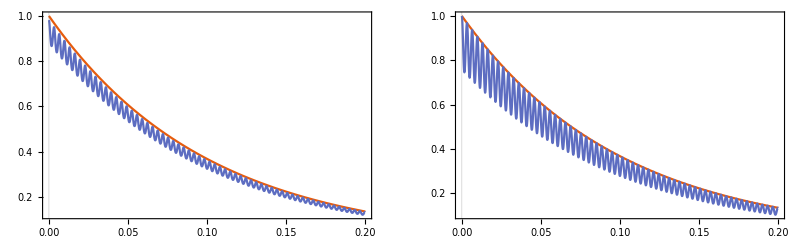

```mathematica
ω:=Sqrt[wSL^2+dw^2]
θ:=ArcTan[dw/wSL]
β:=Pi/2*(1+dB1/100)
wSL:=fSL*2*Pi
dw:=df0*2*Pi
fSL:=500
dB1:=-20
df0:=350
T1p:=0.1
T2p:=0.1
R1p:=1/T1p
R2p:=1/T2p
SLref:=Exp[-t/T1p]
p1:=Plot[{SLref,Abs[CSL]},{t,0,0.2},PlotTheme->"Scientific"]
p2:=Plot[{SLref,Abs[TBSL]},{t,0,0.2},PlotTheme->"Scientific"]
GraphicsGrid[{{p1,p2}},ImageSize->Full]
```

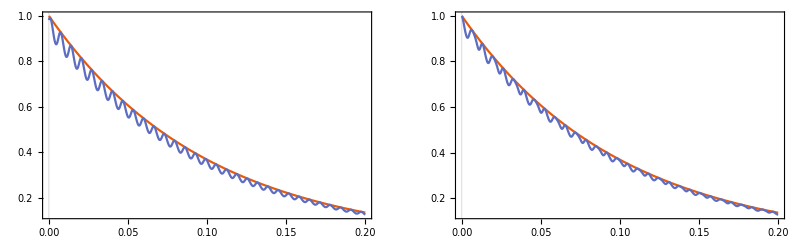

```mathematica
p3:=Plot[{SLref,Abs[TRSL]},{t,0,0.2},PlotTheme->"Scientific"]
p4:=Plot[{SLref,Abs[QRSL]},{t,0,0.2},PlotTheme->"Scientific"]
GraphicsGrid[{{p3,p4}},ImageSize->Full]
```